# AMS-511 Foundations of Quantitative Finance

## Fall 2018 — Assignment 11

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Asian Options

### Overview

An Asian option is one whose value is based on the average price observed rather than the price at expiry. Read the Wikipedia article https://en.wikipedia.org/wiki/Asian_option which describes this derivative in detail.

Consider an Asian arithmetic European put option, its value at time 0 with strike price K and expiry T is

C(T)=max[M[0,T]-K,0]

where M[0,T] is the arithmetic average price over the interval 0≤t≤T defined as

M[0,T]=1/T∫_0^T S(t)ⅆt

Alternately, the option may define the arithmetic average as computed by averaging the price at fixed intervals,

M[0,T]=1/N∑_(i=0)^(N-1) S(t_i)

but here we will only consider the continuous definition above.

Other forms of the Asian option use a different averaging method of computing M[0,T]. For example, the geometric average is sometimes used:

M[0,T]=Exp[∫_0^T Log[S(t)]ⅆt]

Some forms of Asian options have an analytical solution, but the arithmetic case does not. A common means of estimation is Monte Carlo.

### FinancialDerivative[ ]

Mathematica’s FinancialDerivative[ ] function can be used to estimate the value of an Asian arithmetic European put. Here we have S(0)=95.00, K=100.00, T=1, r_f=0.02, and σ=0.10.

```mathematica
FinancialDerivative[{"AsianArithmetic","European","Put"},{"StrikePrice"->100.,"Expiration"->1.,"Inception"->0.,"AverageSoFar"->95.},
{"CurrentPrice"->95.,"Volatility"->0.10,"InterestRate"->0.02}]
```

4.74496

### Monte Carlo

In a Monte Carlo framework the integral above for the average price can be approximated by a discrete sum. Note in the vanilla European case we were able to exploit the solution to the constant coefficient Itô process under the risk-neutral measure:

S(t)=S(0) ⅇ^((r - σ^2/2)t + σ W(t))

where W(t)\[Distributed]N[0,√t].

We can also use this solution to generate a path of prices in time increments of Δ by

S(t+Δ)=S(t) ⅇ^((r - σ^2/2)Δ + σ W(Δ))

where W(Δ)\[Distributed]N[0,√Δ].

Using Mathematica’s notation, the above is

S(t+Δ)=S(t) Exp[(r - σ^2/2)Δ + σ RandomVariate[NormalDistribution[0.,√Δ]]

and once we have generated a sample path i we can compute one realization of the mean:

M^(i)[0,T]=1/(T/Δ+1)∑_(i=0)^(T/Δ) S^(i)(i Δ)

If we repeat this experiment I times then to estimate the mean price

M[0,T]=1/I∑_(i=1)^I M^(i)[0,T]

## Assignment

Create a function that uses Monte Carlo to estimate the value of an Asian arithmetic European put using the same parameters as those in the FinancialDerivative[ ] above. You can use the code developed in Class 10 to help you get started.

```mathematica
xGeneratePrice[nNowPrice_,nVolatility_,nRiskFree_,nTimeStep_]:=nNowPrice Exp[(nRiskFree-nVolatility^2/2.)nTimeStep]Exp[ nVolatility RandomVariate[NormalDistribution[0,√nTimeStep]]]
xAsianArithmeticEuroPutOptMonteCarlo[nNowPrice_,nVolatility_,nStrikePrice_,nExpiry_,nInception_,nRiskFree_,iSamples_,iTimeSteps_]:={Mean[#],StandardDeviation[#]/√iSamples}&[ 
Exp[-nRiskFree nExpiry](Max[nStrikePrice-#,0]&/@(Table[Mean[NestList[xGeneratePrice[#, nVolatility, nRiskFree,nExpiry/iTimeSteps]&,nNowPrice,iTimeSteps]],iSamples]))
];
```

Plot the values of the Monte Carlo simulation for S(0)=80 to 120 in steps of 5 using the other parameter settings above. Compare these estimates to the same using FinancialDerivative[ ].

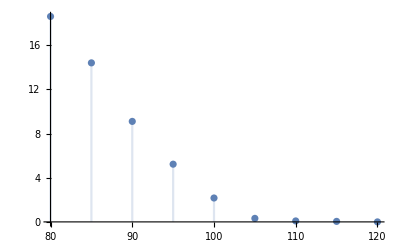

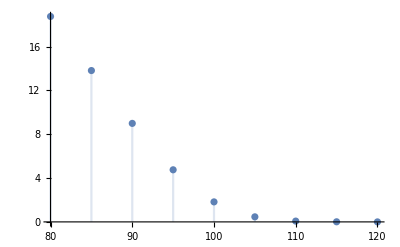

```mathematica
DiscretePlot[First[xAsianArithmeticEuroPutOptMonteCarlo[s,0.1,100,1,0,0.02,100,100]],{s,80,120,5}]
DiscretePlot[FinancialDerivative[{"AsianArithmetic","European","Put"},{"StrikePrice"->100.,"Expiration"->1.,"Inception"->0.,"AverageSoFar"->95.},
{"CurrentPrice"->s,"Volatility"->0.10,"InterestRate"->0.02}],{s,80,120,5}]
```

Both plots have similar trends and the values at each price step are close.